```mathematica
V[t_]:=If[t<1/2.5/2,-51 *Sin[2*Pi*2.5t],0]
```

```mathematica
V[1]
```

0

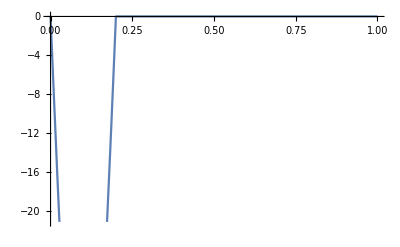

```mathematica
Plot[V[t],{t,0,1}]
```

```mathematica
Samples1=Table[V[(s-1)*1/100],{s,1,51}];
```

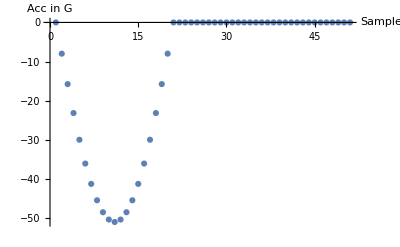

-Graphics-

```mathematica
ListPlot[Samples1,AxesLabel->{"Sample", "Acc in G"}]
```

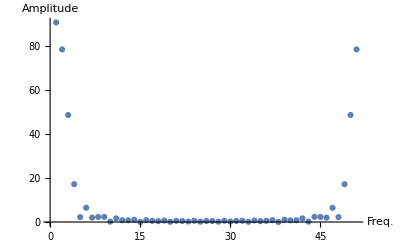

```mathematica
ListPlot[Abs[Fourier[Samples1]],AxesLabel->{"Freq.","Amplitude"}, PlotRange->All]
```

```mathematica
VC[t_]:=Max[V[t],-16]
```

```mathematica
Samples2=Table[VC[(s-1)*1/100],{s,1,51}];
```

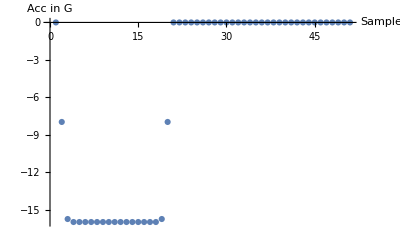

```mathematica
ListPlot[Samples2,AxesLabel->{"Sample", "Acc in G"}]
```

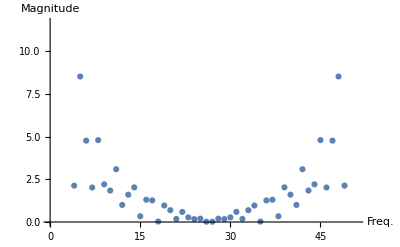

```mathematica
ListPlot[Abs[Fourier[Samples2]],AxesLabel->{"Freq.","Magnitude"}]
```